# St. Petersburg Paradox

## How likely is it that a player will never run out of money?

```mathematica
computeMat[log2nStates_,m_]:=Block[{nStates,weights,dim,mat},
nStates=2^log2nStates;
weights=Table[(p^n(1-p))/.p->0.5,{n,0,Floor[log2nStates]}];
dim={nStates,nStates};

mat=Total[Map[SparseArray[Table[{i,m+i-2^#}->weights[[#+1]],{i,2^#,Min[nStates-m+2^#,nStates]}],dim]&,Range[0,Floor[log2nStates]]]];
mat+=SparseArray[Table[{i,i}->1.,{i,1,m-1}],dim];
Return[mat]
]

computeP[log2nStates_,m_,s_,log2nIter_,mat_]:=Block[{nStates,nIter,P,Pfinal},
nStates=2^log2nStates;
nIter=2^log2nIter;
P=Normal[SparseArray[s->1.,nStates]];
Pfinal=Nest[Dot[mat,#]&,P,nIter];
Return[1.-Sum[Pfinal[[i]],{i,1,m-1}]]
]
```

```mathematica
(*Construct the transition matrix for cost m and state-space size nStates*)
m=2;
nStates=2^10;
mat=computeMat[Log2[nStates],m];
```

```mathematica
(*For a given balance s, apply the Markov matrix nIter times and return the survival probability*)
s=2;
nIter=1000;
survivalProb=computeP[Log2[nStates],m,s,Ceiling[Log2[nIter]],mat]
```

0.252208

```mathematica
(*Compute this probability over a range of m and s, and plot the sol*) 
nStates=2^10;
nIter=1000;
survivalProbs=Flatten[Map[Function[m,With[{mat=computeMat[Log2[nStates],m]},Map[Function[s,{s,m,computeP[Log2[nStates],m,s,Ceiling[Log2[nIter]],mat]}],Range[m,20]]]],Range[2,20]],1];
```

```mathematica
survivalProbsArray=ConstantArray[0,{Max[survivalProbs[[;;,1]]],Max[survivalProbs[[;;,2]]]}];
For[i=1,i≤Length[survivalProbs],i++,survivalProbsArray[[survivalProbs[[i,1]],survivalProbs[[i,2]]]]=survivalProbs[[i,3]]]
```

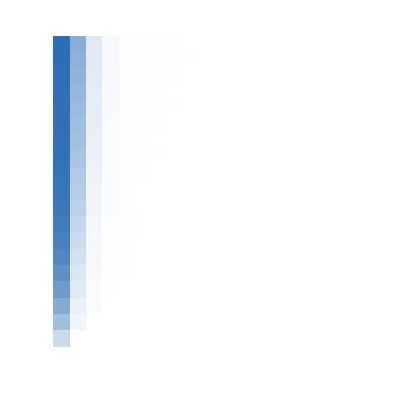

```mathematica
ArrayPlot[survivalProbsArray,DataReversed->True,FrameTicks->{{All,None},{All,None}},FrameLabel->{"s","m"},PlotLegends->{Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Survival Probability"],Below]},ColorFunction->(Blend[{RGBColor["#ffffff"],RGBColor["#2c6eb5"]},#]&),ColorFunctionScaling->False]
```